Q1

```mathematica
nextab[{a_,b_}]:= N[{(a+b)/2, Sqrt[a*b]},200];
m[{a_,b_},n_]:=Nest[nextab, {a,b},n][[1]];
```

```mathematica
w = 2*Integrate[1/Sqrt[1-x^4],{x,0,1}];
N[m[{1, Sqrt[2]},10]-Pi/w,100]
```

0.

Q2

```mathematica
f[x_]:=5^(5*I*x)*Gamma[1-5*I*x]/(Gamma[1-I*x])^5
```

```mathematica
Series[x*f[x], {x,∞,1}]
```

-(√5)/(4 π^2 x)+O[1/x]^2

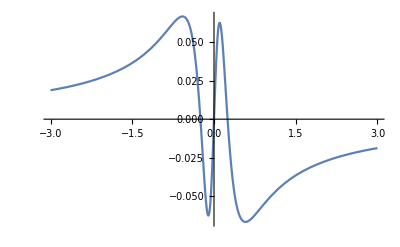

```mathematica
Plot[x/(1-Exp[-2Pi])*Re[f[x]], {x,-3,3}]
```

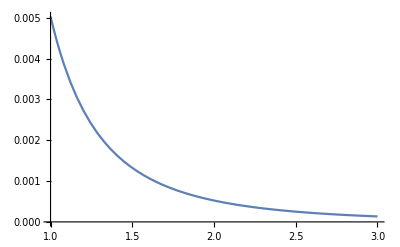

```mathematica
Plot[x/(1-Exp[-2Pi])*Re[f[x]]+(√5)/(4 π^2 x), {x,1,3}]
```

```mathematica
j[d_]:=-(√5)/(4 π^2)Integrate[Cos[d*x]/x, {x,1,∞}];
```

Q3

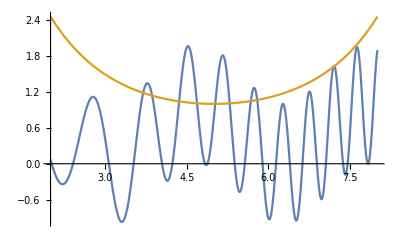

```mathematica
f3[x_]:=Sin[x^2]+Sin[x]^2;
g3[x_]:=Exp[((5-x)^2)/10];
Plot[{f3[x],g3[x]},{x,2,8}]
```

```mathematica
N[Reduce[f3[x]==g3[x] && 3<x<8,x]]
```

x==3.70039||x==3.86421||x==4.36017||x==4.68837||x==5.02256||x==5.28816||x==5.67646||x==5.79265||x==7.19249||x==7.2094

Q4

```mathematica
rmat :=RandomReal[{-1,1},{8,8}];
```

```mathematica
mata = rmat;
matb = rmat;
mata = (mata+Transpose[mata])/2;
matb = (matb+Transpose[matb])/2;
```

```mathematica
m4[t_]:=t*mata+(1-t)*matb;
```

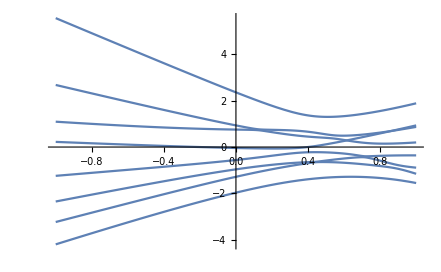

```mathematica
Plot[Sort[Eigenvalues[m4[t]]],{t,-1,1}]
```

Curves do not actually cross

Q5

```mathematica
Cases[Tally[Flatten[Table[x^3+y^3, {x,1,100},{y,x,100}]]],{x_,2}]
```

{{1729,2},{4104,2},{13832,2},{39312,2},{704977,2},{46683,2},{216027,2},{32832,2},{110656,2},{314496,2},{216125,2},{439101,2},{110808,2},{373464,2},{593047,2},{149389,2},{262656,2},{885248,2},{40033,2},{195841,2},{20683,2},{513000,2},{805688,2},{65728,2},{134379,2},{886464,2},{515375,2},{64232,2},{171288,2},{443889,2},{320264,2},{165464,2},{920673,2},{842751,2},{525824,2},{955016,2},{994688,2},{327763,2},{558441,2},{513856,2},{984067,2},{402597,2},{1016496,2},{1009736,2},{684019,2}}

4104